# BPMF Mick Ramsey

## Initial Condition/Import Data

```mathematica
Clear["Global`*"]
Needs["MultivariateStatistics`"]
```

```mathematica
Needs["MultivariateStatistics`"]
```

```mathematica
dim=10; (*Dimension of Latenet Features*)
β0=2.;
W0=N[IdentityMatrix[dim]]; (*Hyperparameter*)
μ0=N[Transpose[{ConstantArray[0,dim]}]];(*Hyperparameter*)
ν0=10. (*Hyperparameter*)
```

10.

```mathematica
Vj=Import["/Users/mick/Desktop/PROJECT/ImportData/movie.csv"];
Ui=Import["/Users/mick/Desktop/PROJECT/ImportData/user.csv"];
matrixdata=Import["/Users/mick/Desktop/PROJECT/ImportData/netflixdata.csv"];
probedata=Import["/Users/mick/Desktop/PROJECT/ImportData/probedata.csv"];
traindata=Import["/Users/mick/Desktop/PROJECT/ImportData/traindata.csv"];
```

```mathematica
spMD=SparseArray[matrixdata];
```

## Equations

```mathematica
uu=probedata[[All,1]]; (*list users in probe data set*)
vv=probedata[[All,2]];(*list of rated movies in probe data set*)
ratings=N[probedata[[All,3]]]; (*Rating cooresponding to user movie combition*)
meanrating=N[Mean[traindata[[All,3]]]];
d=Transpose[spMD]["AdjacencyLists"];
c=spMD["AdjacencyLists"];
rij=ReplaceAll[DeleteCases[0]/@Transpose[matrixdata],{}->ConstantArray[0,1]];
rij2=Select[DeleteCases[0]/@matrixdata,UnsameQ[#,{}]&];

AB[iAB_]:=ReplaceAll[Map[(iAB[[#,All]])&,d],{}->ConstantArray[0,{1,dim}]];
BA[iAB_]:=Map[(iAB[[#,All]])&,c];
AB[iAB_]:=ReplaceAll[Map[(iAB[[#,All]])&,d],{}->ConstantArray[0,{1,dim}]]
BA[iAB_]:=Map[(iAB[[#,All]])&,c]
iW[iAB_]:=With[{Nuv=N[Length[iAB]],Suv=N[Covariance[iAB]],Xuv=N[Transpose[{Mean[iAB]}]]},(Inverse[Inverse[W0]+Nuv Suv+(β0 Nuv)/(β0+Nuv)*(μ0-Xuv).Transpose[μ0-Xuv]]+Transpose[Inverse[Inverse[W0]+Nuv Suv+(β0 Nuv)/(β0+Nuv)*(μ0-Xuv).Transpose[μ0-Xuv]]])/2];
iL[iAB_,Λ_]:=Transpose[CholeskyDecomposition[(Inverse[(β0+N[Length[iAB]])*Λ]+Transpose[Inverse[(β0+N[Length[iAB]])*Λ]])/2]]
iΛuv[iAB_]:=With[{W=iW[iAB],ν=ν0+N[Length[iAB]]},RandomVariate[WishartDistribution[W,ν]]]
iμuv[iAB_,Λ_]:=With[{L=iL[iAB,Λ],μ=(β0 μ0+N[Length[iAB]] N[Transpose[{Mean[iAB]}]])/(β0+N[Length[iAB]])},μ+L.RandomVariate[NormalDistribution[0,1],dim]]
iΛbf[iFG_]:=Inverse[IdentityMatrix[18]+iFG.Transpose[iFG]]
iμbf[iAB_,iFG_]:=With[{μb=iΛbf[iFG].(iFG.Transpose[iAB])},μb+CholeskyDecomposition[iΛbf[iFG]].RandomVariate[NormalDistribution[0,1],18]]
μmean[Λ_,uv_,r_,ΛC_,μC_]:=Λ.(β0*Transpose[uv].(r-meanrating)+ΛC.μC)
Λcovar[uv_,ΛC_]:=(Inverse[ΛC+β0*Transpose[uv].uv]+Transpose[Inverse[ΛC+β0*Transpose[uv].uv]])/2
UVlat[λ_,μm_]:=Flatten[λ.RandomVariate[NormalDistribution[0,1],dim]+μm]

μvmean[Λ_,uv_,r_,g_]:=Λ.(β0*Transpose[uv].(r-meanrating)+g.iμb)
Λvcovar[uv_]:=(Inverse[IdentityMatrix[dim]+β0*(Transpose[uv].uv)]+Transpose[Inverse[IdentityMatrix[dim]+β0*(Transpose[uv].uv)]])/2
```

## Module

```mathematica
Gibbs[data0_,initU0_,initV0_,iterations_]:=
Block[

{initU=initU0,
initV=initV0,
data=data0,
ii=iterations,
iΛu,iΛv,iAB,iμu,iμv,iU0,iV0,iΛ,iα,iλ,id,prediction,proball,counterprobe,rms},
iU0=initU;
iV0=initV;

bArray={};
aArray={};
eArray={};
proball=Total[iV0[[vv]]*iU0[[uu]],{2}]+meanrating ;
counterprobe=1;


Monitor[Do[



iμb=iμbf[Transpose[Vj],GG];

iΛu=iΛuv[Ui];
iμu=iμuv[Ui,iΛu];


Monitor[Do[

iAB=AB[Ui];
iΛ=MapThread[Λvcovar,{iAB}];
iλ=MapThread[CholeskyDecomposition,{iΛ}];
iα=MapThread[μvmean,{iΛ,iAB,rij,G1}];
Vj=MapThread[UVlat,{iλ,iα}];

iBA=BA[Vj];
iΛ=MapThread[Λcovar,{iBA,ConstantArray[iΛu,Dimensions[iBA]]}];
iλ=MapThread[CholeskyDecomposition,{iΛ}];
iα=MapThread[μmean,{iΛ,iBA,rij2,ConstantArray[iΛu,Dimensions[iBA]],ConstantArray[iμu,Dimensions[iBA]]}];
Ui=MapThread[UVlat,{iλ,iα}];

,{tt,1,2}

],{tt,ProgressIndicator[tt,{1,2}]}];

AppendTo[bArray,Vj];
AppendTo[aArray,Ui];


pred=Total[Vj[[aam]]*Ui[[aap]],{2}]+meanrating;
proball=(counterprobe*proball+pred)/(counterprobe+1);
counterprobe=counterprobe+1;
temps=(ratings-proball)^2;
err=(Total[temps]/pairspr)^(1/2);
AppendTo[eArray,err];

,
{t,1,ii}

],{t,ProgressIndicator[t,{1,ii}]}];
]
```

{16781.06003,Null}

## Run

Gibbs[Matrix Data, Prior U, Prior V, Iterations]

```mathematica
Gibbs[matrixdata,Ui,Vj,2]
```

## Results and Graphs

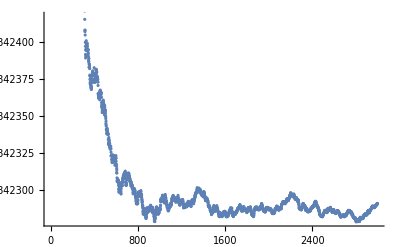

```mathematica
ListPlot[eArray]
```

```mathematica
fu[x_,y_]:={aArray[[x]][[y]]}.Transpose[{aArray[[x]][[y]]}]
fv[x_,y_]:={bArray[[x]][[y]]}.Transpose[{bArray[[x]][[y]]}]
```

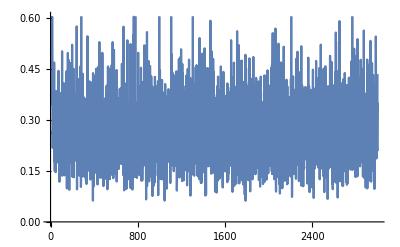

```mathematica
udata=Flatten[Table[fu[x,1],{x,1,3000}]];
ListLinePlot[udata]
```

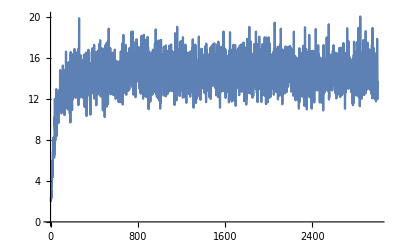

```mathematica
vdata=Flatten[Table[fv[x,2],{x,1,3000}]];
ListLinePlot[vdata]
```

```mathematica
ui[x_,y_,z_]:=aArray[[x]][[y]][[z]]
vi[x_,y_,z_]:=bArray[[x]][[y]][[z]]
```

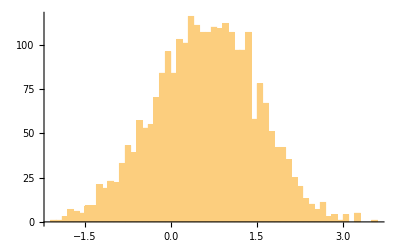

```mathematica
Histogram[Table[vi[x,2567,1],{x,400,3000}],40]
```

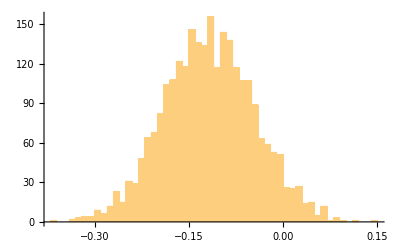

```mathematica
Histogram[Table[ui[x,2567,1],{x,400,3000}],40]
```

```mathematica
Histogram3D[Table[vi[x,323,{2,4}],{x,400,3000}],60]
```

-Graphics3D-

```mathematica
cosine[x1_,x2_]:=({iVArray⟦1800⟧⟦x1⟧}.Transpose[{iVArray⟦1800⟧⟦x2⟧}])/(Norm[iVArray⟦1800⟧⟦x1⟧] Norm[iVArray⟦1800⟧⟦x2⟧])
```

Copyright 2016, Mick Ramsey, All rights reserved